```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Jenna/jennaproject/mma

```mathematica
Needs["Integrals`"]
```

Needs::nocont: Context Integrals` was not created when Needs was evaluated.

```mathematica
mp0=Import["../data/test_matterPower_0.dat","Table"];
trlist=Import["../data/Gru.txt","Table"];
```

```mathematica
size=Dimensions[mp0][[1]]
α=Log[mp0[[2,1]]/mp0[[1,1]]]/Log[mp0[[2,2]]/mp0[[1,2]]]
β=Log[mp0[[size,2]]/mp0[[size-1,2]]]/Log[mp0[[size,1]]/mp0[[size-1,1]]]
```

496

1.03608

-2.44708

```mathematica
Pm=Interpolation[mp0];
tr=Interpolation[trlist];
```

```mathematica
Dimensions[trlist]
```

{140,2}

```mathematica
Pmgood[k_]=If[k<0.0001||k>1.993,0,Pm[k]]
```

If[k<0.0001||k>1.993,0,Pm[k]]

```mathematica
Plot[(1+r^2)/(2r),{r,0,5}];
```

```mathematica
Limit[(r-μ)/(1+r^2-2r*μ)^(1/2),r->1]/.μ->1
```

0

```mathematica
Limit[(3r+7μ-10r*μ^2)/(1+r^2-2r*μ),r->1]/.μ->1
```

13/2

```mathematica
f[r_,μ_]:=If[r==1&&μ==1,13/2,(3r+7μ-10r*μ^2)/(1+r^2-2r*μ)]
g[r_,μ_]:=If[r==1&&μ==1,0,(r-μ)/(1+r^2-2r*μ)^(1/2)]
```

```mathematica
Clear[S]
S=#^3/(2*Pi^2)*(fgps[#,Pmgood]-fgps2[#,Pmgood])&/@Take[mp0,{1,496,20}][[All,1]]
```

Suave::success: Needed 1000 function evaluations on 1 subregions.

Suave::success: Needed 50000 function evaluations on 50 subregions.

General::stop: Further output of Suave will be suppressed during this calculation.

{4.61441×10^-8,2.24386×10^-7,1.08661×10^-6,5.17211×10^-6,0.000024191,0.000108205,0.000478426,0.00197532,0.00762289,0.0285351,0.11607,0.603402,3.86245,22.5877,93.28,239.387,475.892,860.332,1155.72,1315.6,1265.84,1065.34,799.693,544.88,345.193}

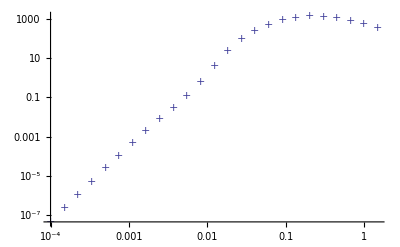

```mathematica
ListLogLogPlot[Thread[{Take[mp0[[All,1]],{1,496,20}],S}],PlotMarkers->"+"]
```